# Spin Dynamics Problem Set

## Question 1D

```mathematica
(* Spin-1 Matrices in natural units (hbar = 1)*)
Sx=1/Sqrt[2] {{0,1,0},{1,0,1},{0,1,0}};
Sy=1/Sqrt[2] {{0,-I,0},{I,0,-I},{0,I,0}};
Sz={{1,0,0},{0,0,0},{0,0,-1}};

Delta=2.87; (* Zero Field Splitting in GHz *)
gamma = -0.0028 (* gyromagnetic ratio in GHz/G *);

bmin = 0 (*minimum B field in Gauss*);
bmax = 1050 (*maximum B field in Gauss *);
```

### 1D with

```mathematica
Hpll = Δ Sz.Sz - γ b Sz ;
energiesBpll=Eigenvalues[Hpll]
```

{0,-b γ+Δ,b γ+Δ}

```mathematica
Eigenvectors[Hpll]
```

{{0,1,0},{1,0,0},{0,0,1}}

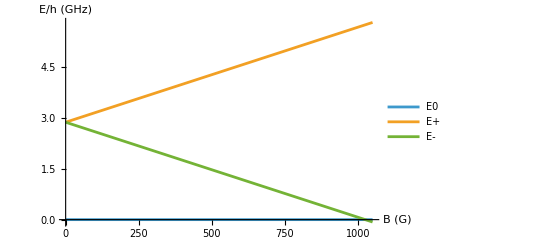

```mathematica
Plot[Evaluate[energiesBpll /. {Δ->Delta, γ->gamma}], {b, bmin, bmax}, PlotLegends->{"E0","E+","E-"},AxesLabel->{"B (G)","E/h (GHz)"}]
```

### 1D with

```mathematica
H=Δ Sz.Sz-γ (Bx Sx+By Sy);
energiesBperp=Eigenvalues[H]//FullSimplify
```

{Δ,1/2 (Δ-√(4 (Bx^2+By^2) γ^2+Δ^2)),1/2 (Δ+√(4 (Bx^2+By^2) γ^2+Δ^2))}

```mathematica
(Eigenvectors[H]// FullSimplify) /.{Bx^2 + By^2 -> B^2}
```

{{1-(2 Bx)/(Bx+ⅈ By),0,1},{(Bx-ⅈ By)/(Bx+ⅈ By),(Δ+√(4 B^2 γ^2+Δ^2))/(√2 (Bx+ⅈ By) γ),1},{(Bx-ⅈ By)/(Bx+ⅈ By),(Δ-√(4 B^2 γ^2+Δ^2))/(√2 (Bx+ⅈ By) γ),1}}

```mathematica
energiesBperp = energiesBperp /. {Bx^2 + By^2 -> B^2}
```

{Δ,1/2 (Δ-√(4 B^2 γ^2+Δ^2)),1/2 (Δ+√(4 B^2 γ^2+Δ^2))}

```mathematica
evalsBperp[b_] := energiesBperp /. {Δ-> Delta, γ->gamma, B->b}
```

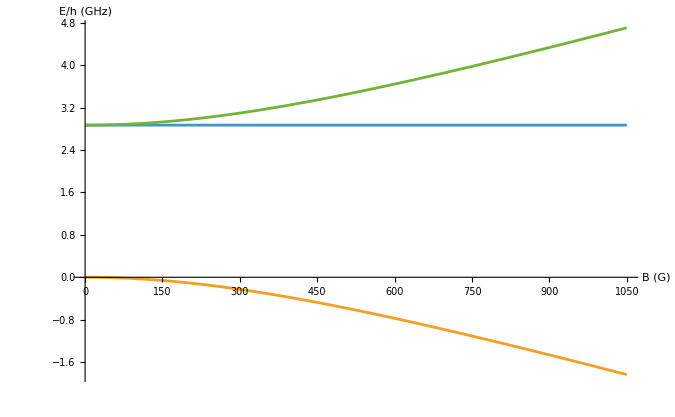

```mathematica
Plot[Evaluate[evalsBperp[b]],{b,bmin,bmax},AxesLabel->{"B (G)","E/h (GHz)"}]
```

### 1D with

```mathematica
ℋ = Δ Sz.Sz - γ B (0.1Sx  + 0.995 Sz  );
MatrixForm[ℋ]
```

(-0.995 B γ+Δ | -0.0707107 B γ | 0.
-0.0707107 B γ | 0. | -0.0707107 B γ
0. | -0.0707107 B γ | 0.995 B γ+Δ)

```mathematica
energiesBalmostZ=Eigenvalues[ℋ] // FullSimplify
```

{Root[0.01 B^2 γ^2 Δ+(-1.00003 B^2 γ^2+Δ^2) #1-2 Δ #1^2+#1^3&,1],Root[0.01 B^2 γ^2 Δ+(-1.00003 B^2 γ^2+Δ^2) #1-2 Δ #1^2+#1^3&,2],Root[0.01 B^2 γ^2 Δ+(-1.00003 B^2 γ^2+Δ^2) #1-2 Δ #1^2+#1^3&,3]}

```mathematica
(*Eigenvectors[ℋ] // FullSimplify*)
```

```mathematica
evalsBalmostZ[b_] := energiesBalmostZ /. {Δ->Delta, γ -> gamma, B->b}
```

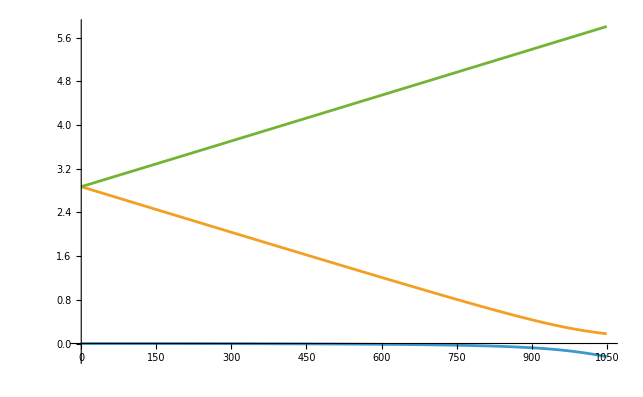

```mathematica
Plot[Evaluate[evalsBalmostZ[b]], {b, bmin, bmax}]
```

## Question 2

```mathematica
dsolved =(DSolve[{a'[t] == I δ/2 a[t] + I Ω / 2 b[t], b'[t] ==- I δ/2 b[t] + I Ω / 2 a[t], a[0] == 1, b[0]==0}, {a[t], b[t]}, t] // FullSimplify)
```

{{a[t]→Cos[1/2 t √(δ^2+Ω^2)]+(ⅈ δ Sin[1/2 t √(δ^2+Ω^2)])/(√(δ^2+Ω^2)),b[t]→(ⅈ Ω Sin[1/2 t √(δ^2+Ω^2)])/(√(δ^2+Ω^2))}}

```mathematica
beta[t_] := b[t] /. First[dsolved];
```

```mathematica
probFlip[t_] := Abs[beta[t]]^2;
probFlip[t]
```

Abs[(Ω Sin[1/2 t √(δ^2+Ω^2)])/(√(δ^2+Ω^2))]^2

### 2D (i) Rabi Oscillations for

```mathematica
Manipulate[Plot[Evaluate[probFlip[t] /. {δ->0, Ω->c} ], {t, 0, 50} ], {c, 0.1, 2}]
```

### 2D (ii) Rabi Oscillations for

```mathematica
Manipulate[Plot[Evaluate[probFlip[t] /. {δ->c, Ω->c} ], {t, 0, 50} ], {c, 0.1, 2}]
```

### 2D (iii) Dependence on detuning at

```mathematica
probF[t_, δ_, Ω_] := Evaluate[probFlip[t] /. {δ->δ, Ω->Ω}]
```

```mathematica
Manipulate[Plot[probF[c, δ, Pi/c], {δ, -2, 2}], {c,0.1, 10}]
```

```mathematica
Sin[Pi/2]
```

1

### 2F Numerically Solving ODE

```mathematica
alphaPrime = I δ/2 (aRe+ I aIm)+ I Ω/2 (1 +E^(-2I v t) )(bRe + I bIm);
betaPrime =  - I δ/2 (bRe + I bIm)+ I Ω/2 (1 +E^(-2I v t) )(aRe + I aIm);
ComplexExpand[Re[alphaPrime]]
ComplexExpand[Im[alphaPrime]]
```

-(aIm δ)/2-(bIm Ω)/2-1/2 bIm Ω Cos[2 t v]+1/2 bRe Ω Sin[2 t v]

(aRe δ)/2+(bRe Ω)/2+1/2 bRe Ω Cos[2 t v]+1/2 bIm Ω Sin[2 t v]

```mathematica
ComplexExpand[Re[betaPrime]]
ComplexExpand[Im[betaPrime]]
```

(bIm δ)/2-(aIm Ω)/2-1/2 aIm Ω Cos[2 t v]+1/2 aRe Ω Sin[2 t v]

-(bRe δ)/2+(aRe Ω)/2+1/2 aRe Ω Cos[2 t v]+1/2 aIm Ω Sin[2 t v]

### 2H Dressed States

```mathematica
Hrwa = {{δ, Ω}, {Ω, -δ}};
eigvens = Eigenvectors[Hrwa]
```

{{-(-δ+√(δ^2+Ω^2))/Ω,1},{-(-δ-√(δ^2+Ω^2))/Ω,1}}

```mathematica
Hrwa.eigvens[[2]]
```

{Ω-(δ (-δ-√(δ^2+Ω^2)))/Ω,√(δ^2+Ω^2)}

```mathematica
eigenenergies2H = Eigenvalues[Hrwa]
```

{-√(δ^2+Ω^2),√(δ^2+Ω^2)}

```mathematica
eigenenergies2Hfunc[d_, O_] := eigenenergies2H /. {δ->d, Ω->O};
eigenenergies2Hfunc[0,1]
```

{-1,1}

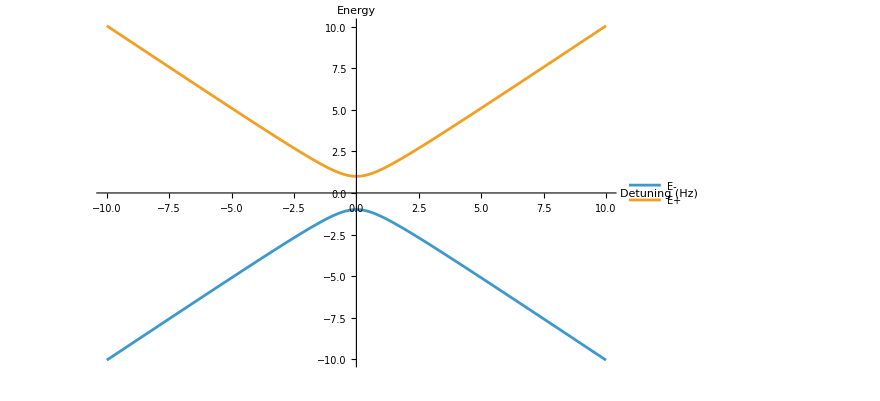

```mathematica
Plot[Evaluate[eigenenergies2Hfunc[d, 1]], {d, -10, 10}, PlotLegends->{"E-","E+"},AxesLabel->{"Detuning (Hz)","Energy"}]
```

### 2J

```mathematica
E2j[B0_, B1_, nu_, t_] := (B0 + B1 Cos[nu t]);
Manipulate[Plot[Evaluate[{E2j[b0, b1,nu, t], -E2j[b0, 1, 1, 10]}], {b0, 0, 10}, PlotLegends->{"E-","E+"},AxesLabel->{"B0 (G)","E/h (GHz)"}], {b1, 0, 4}, {nu, 0.1, 10}, {t, 0, 10}]
```

## Question 3

### 3a

```mathematica
Hrwa3 = I/2 {{δ, Ω Exp[-I θ]}, {Ω Exp[ I θ], -δ}};

eigenEnergies3 = Eigenvalues[Hrwa3];
eigenVecs3 = Eigenvectors[Hrwa3];
```

```mathematica
U3[t_] := MatrixExp[ Hrwa3 t];
U3[t] = FullSimplify[U3[t], Assumptions->{δ, Ω, θ, t} ∈ Reals];
U3[t]
```

{{Cos[1/2 t √(δ^2+Ω^2)]+(ⅈ δ Sin[1/2 t √(δ^2+Ω^2)])/(√(δ^2+Ω^2)),(Ω (ⅈ Cos[θ]+Sin[θ]) Sin[1/2 t √(δ^2+Ω^2)])/(√(δ^2+Ω^2))},{(ⅈ ⅇ^(ⅈ θ) Ω Sin[1/2 t √(δ^2+Ω^2)])/(√(δ^2+Ω^2)),Cos[1/2 t √(δ^2+Ω^2)]-(ⅈ δ Sin[1/2 t √(δ^2+Ω^2)])/(√(δ^2+Ω^2))}}

```mathematica
d3solved =(DSolve[{a'[t] == I δ/2 a[t] + I Ω Exp[- I θ]/ 2 b[t], b'[t] ==- I δ/2 b[t] + I Ω Exp[I θ]/ 2 a[t], a[0] == A0, b[0]==B0}, {a[t], b[t]}, t]) // FullSimplify
```

{{a[t]→(ⅇ^(-1/2 ⅈ (2 θ+t √(δ^2+Ω^2))) (B0 (-1+ⅇ^(ⅈ t √(δ^2+Ω^2))) Ω+A0 ⅇ^(ⅈ θ) ((-1+ⅇ^(ⅈ t √(δ^2+Ω^2))) δ+(1+ⅇ^(ⅈ t √(δ^2+Ω^2))) √(δ^2+Ω^2))))/(2 √(δ^2+Ω^2)),b[t]→(ⅇ^(-1/2 ⅈ t √(δ^2+Ω^2)) (A0 ⅇ^(ⅈ θ) (-1+ⅇ^(ⅈ t √(δ^2+Ω^2))) Ω+B0 (δ-ⅇ^(ⅈ t √(δ^2+Ω^2)) δ+(1+ⅇ^(ⅈ t √(δ^2+Ω^2))) √(δ^2+Ω^2))))/(2 √(δ^2+Ω^2))}}

```mathematica
d3solved[[1]][[1]]
```

a[t]→(ⅇ^(-1/2 ⅈ (2 θ+t √(δ^2+Ω^2))) (B0 (-1+ⅇ^(ⅈ t √(δ^2+Ω^2))) Ω+A0 ⅇ^(ⅈ θ) ((-1+ⅇ^(ⅈ t √(δ^2+Ω^2))) δ+(1+ⅇ^(ⅈ t √(δ^2+Ω^2))) √(δ^2+Ω^2))))/(2 √(δ^2+Ω^2))

```mathematica
U3[t_, O_, d_, th_, OmegaR_] := {{Cos[OmegaR t / 2] + I d/OmegaR Sin[OmegaR t / 2], I O Exp[- I th]/OmegaR Sin[OmegaR t/2]}, 
{I O/OmegaR Exp[I th] Sin[OmegaR t/2], Cos[OmegaR t/2] - I d/OmegaR Sin[OmegaR t/2]}};
U3sub[t_, O_, d_, th_] = U3[t, O, d, th, Sqrt[O^2 + d^2]];
```

```mathematica
U3sub[t, O, d, h]
```

{{Cos[1/2 √(d^2+O^2) t]+(ⅈ d Sin[1/2 √(d^2+O^2) t])/(√(d^2+O^2)),(ⅈ ⅇ^(-ⅈ h) O Sin[1/2 √(d^2+O^2) t])/(√(d^2+O^2))},{(ⅈ ⅇ^(ⅈ h) O Sin[1/2 √(d^2+O^2) t])/(√(d^2+O^2)),Cos[1/2 √(d^2+O^2) t]-(ⅈ d Sin[1/2 √(d^2+O^2) t])/(√(d^2+O^2))}}

### 3b(i)

```mathematica
U3sub[t, Pi/(2 t), 0, 0] // FullSimplify
```

{{1/(√2),ⅈ/(√2)},{ⅈ/(√2),1/(√2)}}

```mathematica
U3sub[t, Pi/t, 0, 0] // FullSimplify
```

{{0,ⅈ},{ⅈ,0}}

### 3b(ii)

```mathematica
U3sub[t, Pi/(2 t), 0, Pi/2] // FullSimplify
```

{{1/(√2),1/(√2)},{-1/(√2),1/(√2)}}

```mathematica
U3sub[t, Pi/t,0, Pi/2] // FullSimplify
```

{{0,1},{-1,0}}

```mathematica
U3pix2 = U3sub[t, Pi/(2 t), 0, 0] // FullSimplify;
U3piy2 = U3sub[t, Pi/(2 t), 0, Pi/2] // FullSimplify;
UramseyApx = U3pix2.U3sub[t, 0, d, th].U3pix2  // FullSimplify
```

{{ⅈ Sin[(d t)/2],ⅈ Cos[(d t)/2]},{ⅈ Cos[(d t)/2],-ⅈ Sin[(d t)/2]}}

```mathematica
probRamsey0to1=Abs[UramseyApx[[2]][[1]]]^2
```

Abs[Cos[(d t)/2]]^2

```mathematica
Manipulate[Plot[Cos[d t /2]^2, {t, 0, 10}],{d, -2, 2}]
```

```mathematica
Upix2Tpiy2 = U3piy2.U3sub[t, 0, d, th].U3pix2  // FullSimplify
```

{{(1/2+ⅈ/2) (Cos[(d t)/2]+Sin[(d t)/2]),(1/2+ⅈ/2) (Cos[(d t)/2]-Sin[(d t)/2])},{(-1/2+ⅈ/2) (Cos[(d t)/2]-Sin[(d t)/2]),(1/2-ⅈ/2) (Cos[(d t)/2]+Sin[(d t)/2])}}

```mathematica
U3piy2
```

{{1/(√2),1/(√2)},{-1/(√2),1/(√2)}}

### 3E

```mathematica
UramseyEx[T_,tau_]:=U3sub[tau,Pi/(2 tau),d,h].U3sub[T,0,d,h].U3sub[tau,Pi/(2 tau),d,h]//FullSimplify

P1exact[T_,tau_]:=Abs[UramseyEx[T,tau][[2,1]]]^2//FullSimplify

P1exact[T,tau]
```

1/4 ⅇ^(-2 Im[h]) π^2 Abs[(-8 d tau Sin[(d T)/2] Sin[1/4 √(4 d^2+π^2/tau^2) tau]^2+√(4 d^2+π^2/tau^2) tau Csc[(d T)/2] Sin[d T] Sin[1/2 √(4 d^2+π^2/tau^2) tau])/(π^2+4 d^2 tau^2)]^2

```mathematica
tauVal=Pi/(2); 
(*P1numeric[T_,dVal_]:=P1exact[T,tauVal]/. {d->dVal,h->0}//N
Plot[P1numeric[T,0.2],{T,0,30},PlotRange->{0,1},AxesLabel->{"T (wait time)","P(0→1)"},PlotLabel->"Exact Ramsey Fringe, δ=0.2"]*)
```

```mathematica
UramseyEx[T, t]
```

{{(ⅇ^(-1/2 ⅈ d T) ((-1+ⅇ^(ⅈ d T)) π^2+(π^2+ⅇ^(ⅈ d T) (π^2+8 d^2 t^2)) Cos[1/2 √(π^2+4 d^2 t^2)]+4 ⅈ d ⅇ^(ⅈ d T) t √(π^2+4 d^2 t^2) Sin[1/2 √(π^2+4 d^2 t^2)]))/(2 (π^2+4 d^2 t^2)),(2 ⅈ ⅇ^(-ⅈ h) π t Sin[1/4 √(4 d^2+π^2/t^2) t] (√(4 d^2+π^2/t^2) Cos[1/4 √(4 d^2+π^2/t^2) t] Cos[(d T)/2]-2 d Sin[1/4 √(4 d^2+π^2/t^2) t] Sin[(d T)/2]))/(π^2+4 d^2 t^2)},{(2 ⅈ ⅇ^(ⅈ h) π t Sin[1/4 √(4 d^2+π^2/t^2) t] (√(4 d^2+π^2/t^2) Cos[1/4 √(4 d^2+π^2/t^2) t] Cos[(d T)/2]-2 d Sin[1/4 √(4 d^2+π^2/t^2) t] Sin[(d T)/2]))/(π^2+4 d^2 t^2),(ⅇ^(-1/2 ⅈ d T) (-((-1+ⅇ^(ⅈ d T)) π^2)+((1+ⅇ^(ⅈ d T)) π^2+8 d^2 t^2) Cos[1/2 √(π^2+4 d^2 t^2)]-4 ⅈ d t √(π^2+4 d^2 t^2) Sin[1/2 √(π^2+4 d^2 t^2)]))/(2 (π^2+4 d^2 t^2))}}

{h→0,d→0.628319,tau→3}

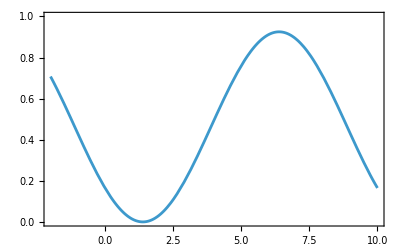

```mathematica
flags = {h-> 0, d-> .1*2Pi, tau-> 3}
Plot[1/4 ⅇ^(-2 Im[h]) π^2 Abs[(-8 d tau Sin[(d T)/2] Sin[1/4 √(4 d^2+π^2/tau^2) tau]^2+√(4 d^2+π^2/tau^2) tau Csc[(d T)/2] Sin[d T] Sin[1/2 √(4 d^2+π^2/tau^2) tau])/(π^2+4 d^2 tau^2)]^2/.flags, {T, -2, 10}, PlotRange-> {0,1}, Frame-> True]
```